# QIF: Numerical Simulations

## Synaptic activation

```mathematica
Refine[Integrate[HeavisideTheta[τ-(t-p)]/τ*DiracDelta[p-k],{p,-Infinity,t}],{k∈Reals, t∈Reals}]
```

(HeavisideTheta[-k+t] HeavisideTheta[k-t+τ])/τ

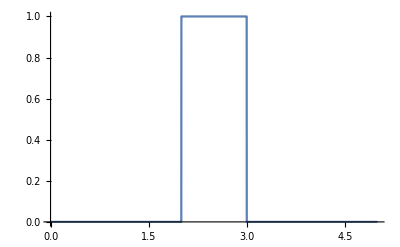

```mathematica
Plot[(HeavisideTheta[-k+t] HeavisideTheta[k-t+τ])/τ/.k->2/.τ->1,{t,0,5}]
```